#### Potencial que tem os autoestados do par quark-antiquark real https://community.wolfram.com/groups/-/m/t/3311726

```mathematica
ClearAll["Global`*"]
```

```mathematica
(*       Criacao 1 par q-qbar real   *)
Niveis={134.97,547.86,1019.46,3096.91,9460.3};
NumNiveis=5;

PotxMax=20.0;
xmax=0.5;
NumRegArq=500;
xstep=(2.0*xmax)/NumRegArq;
PorcCorte=0.95;
ListaCorte={};
```

```mathematica
dressingTransformationPotentials[evals_,xMax_,opts___]:=Module[{ε,f,g,evals1=Sort[evals]-Max[evals],W=0&},Do[ε=evals1[[-k]];
W=NDSolveValue[{f'[x]-f[x]^2+W[x]==ε,f[0]==0,g'[x]==4 f[x] f'[x]-W'[x],g[0]==2 ε-W[0]},{f,g},{x,0,xMax},opts][[2]],{k,2,Length[evals1]}];
Function@@{ξ,W[ξ]+Max[evals]}]
```

#### Loop varredura acumulando niveis

```mathematica
matout=OpenWrite["ResHEP1.csv"];
```

==========   Numero de niveis calculados:2==========

Raio do poco para PotCorte=520.467 xCorte=0.116

Potencial obtido:

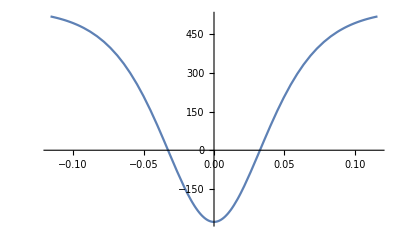

Niveis experimentais:

{134.97,547.86}

Eigensystem::maxit2: Warning: maximum number of iterations, 1000, has been reached by the Arnoldi algorithm without convergence to the specified tolerance, but the current best computed value has been returned. You can use method options with Method -> {Arnoldi, opts} to increase the size of basis vectors, the maximum number of iterations, reduce the tolerance, or use an estimate as a shift, any of which may help.

Eigensystem::chnpdef: Warning: there is a possibility that the second matrix SparseArray[«1»] in the first argument is not positive definite, which is necessary for the Arnoldi method to give accurate results.

Niveis obtidos pela solucao eq Schrodinger com este potencial:

{134.97,547.891}

Funcoes de onda obtidas e potencial:

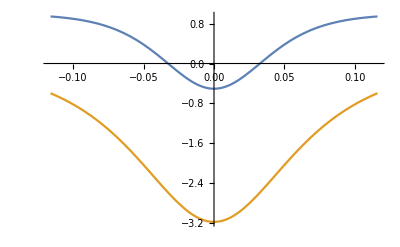
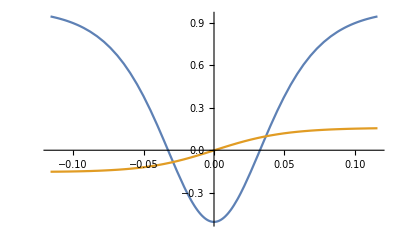

==========   Numero de niveis calculados:3==========

Raio do poco para PotCorte=968.487 xCorte=0.144

Potencial obtido:

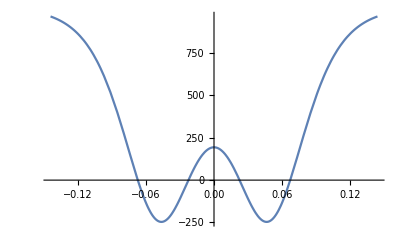

Niveis experimentais:

{134.97,547.86,1019.46}

Eigensystem::maxit2: Warning: maximum number of iterations, 1000, has been reached by the Arnoldi algorithm without convergence to the specified tolerance, but the current best computed value has been returned. You can use method options with Method -> {Arnoldi, opts} to increase the size of basis vectors, the maximum number of iterations, reduce the tolerance, or use an estimate as a shift, any of which may help.

Eigensystem::chnpdef: Warning: there is a possibility that the second matrix SparseArray[«1»] in the first argument is not positive definite, which is necessary for the Arnoldi method to give accurate results.

Niveis obtidos pela solucao eq Schrodinger com este potencial:

{134.97,547.86,1019.52}

Funcoes de onda obtidas e potencial:

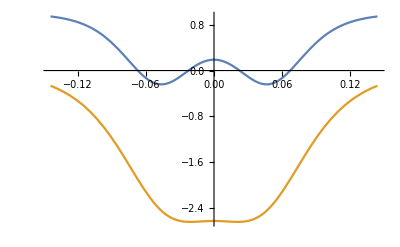
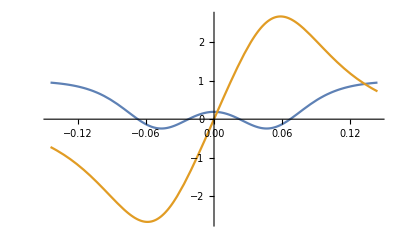
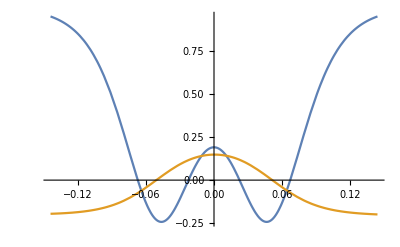

==========   Numero de niveis calculados:4==========

Raio do poco para PotCorte=2942.06 xCorte=0.118

Potencial obtido:

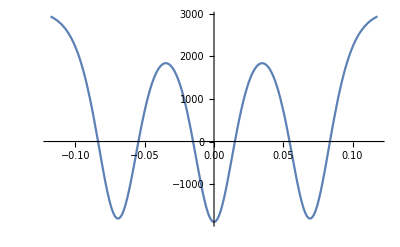

Niveis experimentais:

{134.97,547.86,1019.46,3096.91}

Eigensystem::maxit2: Warning: maximum number of iterations, 1000, has been reached by the Arnoldi algorithm without convergence to the specified tolerance, but the current best computed value has been returned. You can use method options with Method -> {Arnoldi, opts} to increase the size of basis vectors, the maximum number of iterations, reduce the tolerance, or use an estimate as a shift, any of which may help.

General::stop: Further output of Eigensystem::maxit2 will be suppressed during this calculation.

Eigensystem::chnpdef: Warning: there is a possibility that the second matrix SparseArray[«1»] in the first argument is not positive definite, which is necessary for the Arnoldi method to give accurate results.

General::stop: Further output of Eigensystem::chnpdef will be suppressed during this calculation.

Niveis obtidos pela solucao eq Schrodinger com este potencial:

{134.985,547.876,1019.48,3097.12}

Funcoes de onda obtidas e potencial:

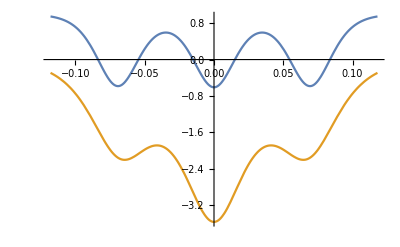
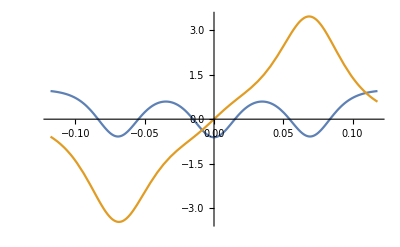
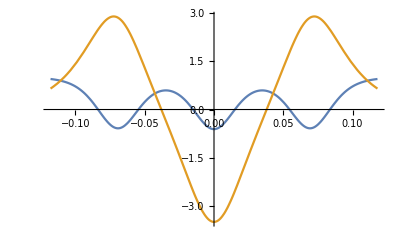
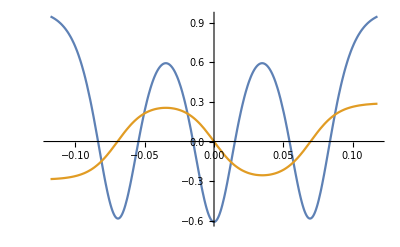

==========   Numero de niveis calculados:5==========

Raio do poco para PotCorte=8987.28 xCorte=0.09

Potencial obtido:

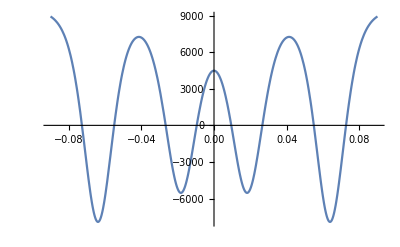

Niveis experimentais:

{134.97,547.86,1019.46,3096.91,9460.3}

Niveis obtidos pela solucao eq Schrodinger com este potencial:

{135.465,548.591,1020.13,3097.55,9461.52}

Funcoes de onda obtidas e potencial:

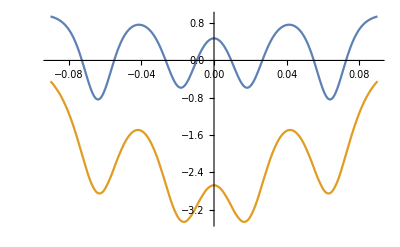
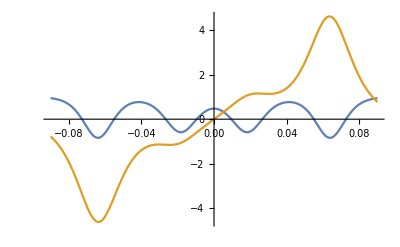
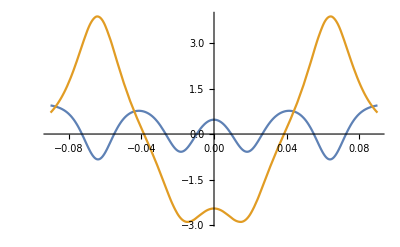
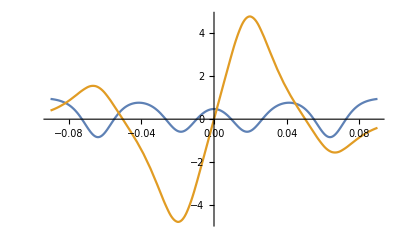
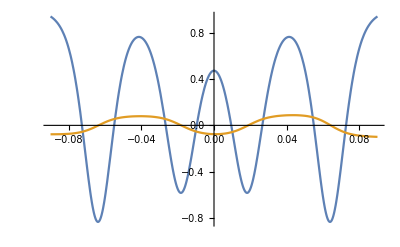

==========   Raio da bolha x Energia   ===========

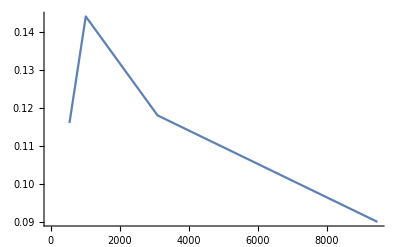

ResHEP1.csv

```mathematica
For[NivCalc=2,NivCalc≤NumNiveis,NivCalc++,
NivElem=Take[Niveis,NivCalc];
PotCorte=Evaluate[PorcCorte*Niveis[[NivCalc]]];

Print["==========   Numero de niveis calculados:",NivCalc,"=========="];
V=dressingTransformationPotentials[NivElem,PotxMax];
xCorte=PotxMax;
While [(xCorte>0.0)&&(PotCorte<V[xCorte]),xCorte=xCorte-xstep];
Print["Raio do poco para PotCorte=",PotCorte," xCorte=",xCorte];
ListaCorte=Append[ListaCorte,{NivElem[[NivCalc]],xCorte}];
Print["Potencial obtido:"];
Print[Plot[V[Abs[x]],{x,-xCorte,xCorte},PlotRange->All]];
Print["Niveis experimentais:"];
Print[NivElem];
ndse=NDEigensystem[-ψ''[x]+V[Abs[x]] ψ[x],ψ,{x,-PotxMax,PotxMax},NivCalc,Method->{"SpatialDiscretization"->{"FiniteElement",{"MeshOptions"->{"MaxCellMeasure"->0.005}}}}];
Print["Niveis obtidos pela solucao eq Schrodinger com este potencial:"];
Print[ndse[[1]]];
Print["Funcoes de onda obtidas e potencial:"];
Print[Table[Plot[{V[Abs[x]]/Niveis[[NivCalc]], Evaluate[ndse[[2,j]][x]]},{x,-xCorte,xCorte},PlotRange->All],{j,1,NivCalc}]];
WriteString[matout,"\n===== Nivel maximo ",ToString[NivCalc,InputForm]," =====; \n"];
WriteString[matout,"Energia=; ",ToString[Niveis[[NivCalc]],InputForm],"; \n"];
WriteString[matout,"xCorte=; ",ToString[xCorte,InputForm],"; \n\n"];
lista={"x; Pot; "};
For[i=1,i<=NivCalc,i++,lista=Append[lista,StringJoin["Psi",ToString[i,InputForm],"; "]]];
lista=Append[lista,"\n"];
Cabec=StringJoin[lista];
WriteString[matout,Cabec];
Do[
lista={};
lista=Append[lista,StringJoin[ToString[x,InputForm],"; ",ToString[V[Abs[x]],InputForm],"; "]];
For[i=1,i<=NivCalc,i++,lista=Append[lista,StringJoin[StringJoin[ToString[ndse[[2,i]][x],InputForm],"; "]]]];
lista=Append[lista,"\n"];
Cabec=StringJoin[lista];
WriteString[matout,Cabec],{x,-xCorte,xCorte,xCorte/NumRegArq}];

]
Print["==========   Raio da bolha x Energia   ==========="]
ListPlot[ListaCorte,Joined->True]
WriteString[matout,"\n===== Raio da bolha x Energia ===== \nRaio; Energia; \n"];
For[i=1,i<NumNiveis,i++,WriteString[matout,ToString[ListaCorte[[i,1]],InputForm],"; ",ToString[ListaCorte[[i,2]],InputForm],"; \n"]];
Close[matout]
```